```mathematica
Zdol=s*L+r2+R
```

151.62+0.01968 s

```mathematica
1/(1/(1.62+0.01968 s)+2.2*^-6 s)
```

```mathematica
Zgora=Rg+1/(s*c)
```

50+(2.12766×10^6)/s

```mathematica
k=FullSimplify[Zdol/(Zdol+Zgora)]
```

(s (7704.27+1. s))/(1.08113×10^8+s (10244.9+1. s))

```mathematica
impulseresponse=Simplify[TrigReduce[ComplexExpand[Simplify[InverseLaplaceTransform[k, s, t]]]]]
```

1. ⅇ^(-5122.46 t) (-2540.65 Cos[(9048.38+0. ⅈ) t]+1. DiracDelta[t]-10510. Sin[(9048.38+0. ⅈ) t])

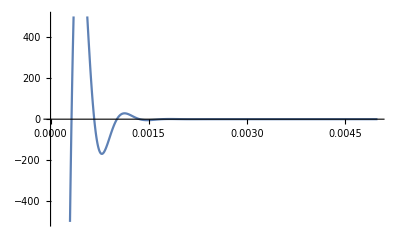

```mathematica
Plot[impulseresponse,{t, 0, 0.005}, PlotRange->{-500,500}]
```

```mathematica
stepresponse=Simplify[TrigReduce[ComplexExpand[Simplify[InverseLaplaceTransform[k/s, s, t]]]]]
```

ⅇ^(-5122.46 t) (1. Cos[(9048.38+0. ⅈ) t]+0.285334 Sin[(9048.38+0. ⅈ) t])

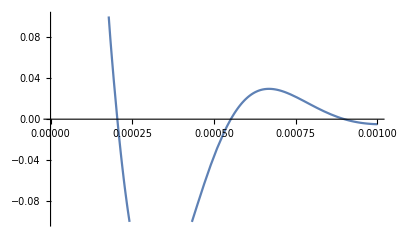

```mathematica
Plot[stepresponse,{t, 0,0.001}, PlotRange->{-0.1,0.1}]
```

```mathematica
R=150
```

150

```mathematica
r2=1.62
```

1.62

```mathematica
c=0.47*10^-6
```

4.7×10^-7

```mathematica
L=19.68*10^-3
```

0.01968

```mathematica
Rg=50
```

50

```mathematica
Simplify[ComplexExpand[impulseresponse]]
```

ⅇ^(-187.786 t) (Sin[0.-4804.76 t] ((3.21862+146.628 ⅈ)-(3.21862-146.628 ⅈ) Cos[(9609.52+0. ⅈ) t]-(146.628+3.21862 ⅈ) Sin[(9609.52+0. ⅈ) t])+Cos[(4804.76+0. ⅈ) t] ((146.628-3.21862 ⅈ)+(146.628+3.21862 ⅈ) Cos[(9609.52+0. ⅈ) t]-(3.21862-146.628 ⅈ) Sin[(9609.52+0. ⅈ) t]))

```mathematica
Zdoldrugie=((r2+I*w*L)^-1+I*w*c )^-1
kdrugie=FullSimplify[Zdol/(Zdol+R)]
```

1/(1/(1.62+(0.+0.01968 ⅈ) w)+(0.+2.2×10^-6 ⅈ) w)

(-24139.9-(0.+293.255 ⅈ) w)/(-2.3121×10^7+w ((0.-375.572 ⅈ)+1. w))

```mathematica
ExpandDenominator[kdrugie]
```

(-24139.9-(0.+293.255 ⅈ) w)/(-2.3121×10^7-(0.+375.572 ⅈ) w+1. w^2)